# Sphere-Plane Near Field Hydrodynamics

## Tabulation Parameters

```mathematica
Npoints = 1000;
ξmin = 10^-3;
ξmax = 10^3;
```

## (1) Translation normal to the plane surface

### Exact (Brenner, Chem. Eng. Sci. 1961, 16, 242)

```mathematica
XA[ξ_?NumericQ]:=Module[{α,n,error,nMax},
α=N[ArcCosh[ξ+1]];
error = 10^-10;
nMax = Ceiling[1-Log[error]/(2 α)];
4/3 NSum[(n(n+1)Sinh[α])/((2n-1)(2n+3))((2Sinh[(2n+1)α]+(2n+1)Sinh[2α])/(4 Sinh[(n+1/2)α]^2-(2n+1)^2 Sinh[α]^2)-1),{n,1,nMax},NSumTerms->nMax]];
```

### Lubrication

```mathematica
XAnf[ξ_?NumericQ]=1/ξ-1/5 Log[ξ]+0.97128;
```

### Tabulate Data

```mathematica
XAdata = ParallelTable[{10^s,XA[10^s]},{s,Log10[ξmin],Log10[ξmax],(Log10[ξmax]-Log10[ξmin])/(Npoints-1)}];
```

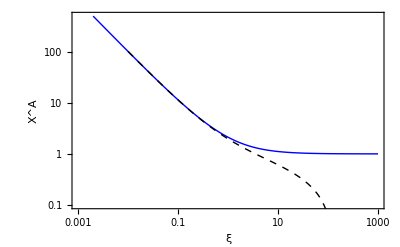

```mathematica
Show[
ListLogLogPlot[XAdata,
Joined->True,
Frame->True,
PlotStyle->{Blue},
PlotRange->{{ξmin,ξmax},{0.1,500}},
FrameLabel->{Style["ξ",FontFamily->"TimesNewRoman",20],Style["X^A",FontFamily->"TimesNewRoman",20]},
FrameTicksStyle->Directive[FontFamily->"TimesNewRoman",14]],

LogLogPlot[XAnf[ξ],{ξ,10^-2,10^2},
PlotStyle->{Black,Dashed}]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["XA.txt",N[XAdata ],{"TSV","Data"}]
```

XA.txt

## (2) Translation parallel to the plane surface

### See MATLAB file.

## (3) Rotation normal to the plane surface

### Exact (G. B. Jeffrey, Proc. London Math. Soc., 1915, 14, 327–338)

```mathematica
XC[ξ_?NumericQ]:=Module[{α,β,n,error,nMax},
α=ArcCosh[ξ+1];
β=Sinh[α];
error=10^-10;
nMax=Ceiling[-Log[error]/(3α)];
4/3 β^3 NSum[Csch[(n+1)α]^3,{n,0,nMax},NSumTerms->nMax]];
```

### Lubrication

```mathematica
XCnf[ξ_?NumericQ]=4/3(Zeta[3]+1/2 ξ Log[ξ]);
```

### Plot

```mathematica
XCdata = ParallelTable[{10^s,XC[10^s]},{s,Log10[ξmin],Log10[ξmax],(Log10[ξmax]-Log10[ξmin])/(Npoints-1)}];
```

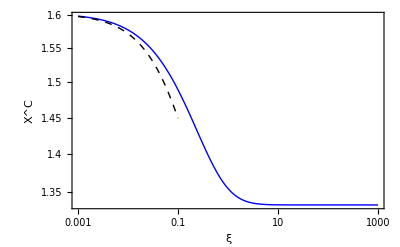

```mathematica
Show[
ListLogLogPlot[XCdata,
Joined->True,
Frame->True,
PlotStyle->{Blue},
PlotRange->Full,
FrameLabel->{Style["ξ",FontFamily->"TimesNewRoman",20],Style["X^C",FontFamily->"TimesNewRoman",20]},
FrameTicksStyle->Directive[FontFamily->"TimesNewRoman",14]],

LogLogPlot[XCnf[ξ],{ξ,10^-3,10^-1},
PlotStyle->{Black,Dashed}]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["XC.txt",N[XCdata],"TSV"]
```

XC.txt

## (4) Rotation parallel to the plane surface

### See MATLAB file.